## Convergencia Mie-CST

```mathematica
saveTask=CreateScheduledTask[FrontEndExecute[FrontEndToken["Save"]],15*60]; (*Saves nb each 15 minutes*)
StartScheduledTask[saveTask]
```

ScheduledTaskObject[…]

## Paquetes a importar

```mathematica
Needs["MaTeX`"] (*Importa la paquetería de LaTeX*)
SetOptions[MaTeX, "Preamble" -> {"\\usepackage{xcolor}"}]
```

{BasePreamble→{\usepackage{lmodern,exscale},\usepackage{amsmath,amssymb}},Preamble→{\usepackage{xcolor}},DisplayStyle→True,ContentPadding→True,LineSpacing→{1.2,0},FontSize→12,Magnification→1,LogFileFunction→None,TeXFileFunction→None}

```mathematica
(*Directorio donde están las paqueterías*)
SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Programas\\Packages"]

Needs["MieTheory`"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Programas\Packages

```mathematica
<< "MieTheory.wl"
```

## Definiciones

```mathematica
h=4.135667696*10^(-15); (*eV s*) (*Constante de Planck*)
hbar=6.582119569*10^(-16); (*eV s*)(*Constante de Planck reducida*)
c=299792458*^9 (*nm s^-1*)(*Velocidad de la luz*);

omega10=Range[0,10,0.01]; 
omegaVis=Range[2,3.1,0.01];
energyTicksMajorVisible={2.07,2.26,2.48,2.76,3.1};

epsPlasma=1.823;


(*Colores*)
blueUNAM=RGBColor[6/255,151/255,213/255];
redUNAM=RGBColor[232/255,68/255,42/255];
gris=RGBColor[127/255,146/255,151/255];
colors2={blueUNAM, redUNAM}
color5={Orange}
colors=(("DefaultPlotStyle"/.(Method/. Charting`ResolvePlotTheme["Scientific",ListLinePlot]))/. Directive[x_,__]:>x)
rojos=Table[RGBColor[1,g,0],{g,0,0.9,0.16}]
sunsetColors=Table[ColorData["SunsetColors"][i],{i,0,0.8,1/7}]
solarColors=Table[ColorData["SolarColors"][i],{i,0,0.8,1/7}]
alpineColors=Table[ColorData["AlpineColors"][i],{i,0,0.8,1/7}]
lakeColors=Table[ColorData["LakeColors"][i],{i,0,0.8,1/7}]
candyColors=Table[ColorData["CandyColors"][i],{i,0,0.8,1/7}]
verde=RGBColor[150/255,200/255,60/255]
```

{RGBColor[Rational[2, 85], Rational[151, 255], Rational[71, 85]],RGBColor[Rational[232, 255], Rational[4, 15], Rational[14, 85]]}

{RGBColor[1, 0.5, 0]}

{RGBColor[0.9, 0.36, 0.054],RGBColor[0.365248, 0.427802, 0.758297],RGBColor[0.945109, 0.593901, 0.],RGBColor[0.645957, 0.253192, 0.685109],RGBColor[0.285821, 0.56, 0.450773],RGBColor[0.7, 0.336, 0.],RGBColor[0.491486, 0.345109, 0.8],RGBColor[0.71788, 0.568653, 0.],RGBColor[0.70743, 0.224, 0.542415],RGBColor[0.287228, 0.490217, 0.664674],RGBColor[0.982289285128704, 0.5771321368979874, 0.011542503255145636],RGBColor[0.5876740325800278, 0.2877284499870081, 0.7500695697462922],RGBColor[0.4262088601796793, 0.5581552810007578, 0.2777996730417023],RGBColor[0.9431487543762861, 0.414555896337833, 0.07140829055870854],RGBColor[0.41497437140121635, 0.393632147507352, 0.7842993779115092]}

{RGBColor[1, 0., 0],RGBColor[1, 0.16, 0],RGBColor[1, 0.32, 0],RGBColor[1, 0.48, 0],RGBColor[1, 0.64, 0],RGBColor[1, 0.8, 0]}

{RGBColor[0., 0., 0.],RGBColor[0.3195368571428571, 0.1164, 0.4341454285714286],RGBColor[0.6695744285714286, 0.22438285714285713, 0.338128],RGBColor[0.8974812857142858, 0.3693308571428571, 0.1452665142857143],RGBColor[0.9882154285714286, 0.5505617142857143, 0.08483494285714285],RGBColor[1., 0.7397017142857143, 0.23300614285714283]}

{RGBColor[0.468742, 0., 0.0158236],RGBColor[0.6706774285714285, 0.06984285714285714, 0.009042057142857144],RGBColor[0.8432481428571429, 0.15849014285714286, 0.008003357142857142],RGBColor[0.9277247142857143, 0.30355071428571423, 0.024193185714285713],RGBColor[0.978545, 0.4534661428571428, 0.0459689],RGBColor[0.995709, 0.6082364285714286, 0.07333049999999999]}

{RGBColor[0.277546, 0.355398, 0.484215],RGBColor[0.3092687142857143, 0.43180485714285716, 0.45451742857142857],RGBColor[0.35382528571428573, 0.4807017142857143, 0.3698534285714286],RGBColor[0.43932542857142853, 0.5335538571428571, 0.38461414285714285],RGBColor[0.5610134285714286, 0.5994675714285714, 0.49026099999999995],RGBColor[0.6995328571428572, 0.6994642857142856, 0.6226554285714285]}

{RGBColor[0.293416, 0.0574044, 0.529412],RGBColor[0.40930385714285716, 0.25890179999999996, 0.6923064285714285],RGBColor[0.5251917142857143, 0.46039919999999995, 0.8552008571428571],RGBColor[0.6206238571428572, 0.6188315714285714, 0.9107938571428571],RGBColor[0.7058281428571428, 0.7557314285714285, 0.9127361428571429],RGBColor[0.7881374285714285, 0.8555037142857143, 0.9026041428571429]}

{RGBColor[0.405188, 0.204349, 0.343389],RGBColor[0.6033010000000001, 0.22473442857142858, 0.36270257142857143],RGBColor[0.7647998571428571, 0.3022755714285714, 0.4413708571428571],RGBColor[0.8306595714285715, 0.45290014285714286, 0.5840857142857143],RGBColor[0.7940618571428572, 0.5946167142857143, 0.7287942857142857],RGBColor[0.7161124285714285, 0.7039788571428571, 0.8368194285714285]}

RGBColor[Rational[10, 17], Rational[40, 51], Rational[4, 17]]

## Funciones

```mathematica
dataQext[dataCabs_,dataCsca_]:=Module[{dataCext},
dataCext=Transpose[{dataCabs[[All,1]],dataCabs[[All,2]]+dataCsca[[All,2]]}]]

errorAbs[data1_,data2_]:=Module[{error},
error=Abs[data1-data2]]

errorRel[data1_,data2_]:=Module[{error},
error=100*Abs[data1-data2]/data2]
```

## Gráficas

```mathematica
plotStyling = {PlotRange -> All,
   PlotStyle -> (Directive[#, Thickness[0.003]] & /@ sunsetColors),  
   Frame -> True,
   FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
   LabelStyle->{FontFamily->"Latin Modern Roman 10"},
   ImagePadding->{{90,10},{60,60}}};
  
  
  SetDirectory["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\Figuras\\3-FIT"]
```

C:\Users\danal\Documents\Github\Tesis-de-Licenciatura\Figuras\3-FIT

## Índice de refracción usado en CST

```mathematica
datosIM=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\Funciones_dielectricas\\CST\\epsEritrocitosData30_Im_Fit.csv"];
datosRE=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\Funciones_dielectricas\\CST\\epsEritrocitosData30_Re_Fit.csv"];

(*Se pasa de longitudes de onda a energías y se toma a la primera columna como el vector de energías*)
parteImFit=Interpolation[Transpose[{datosIM[[All,1]],datosIM[[All,2]]}]];
parteReFit=Interpolation[Transpose[{datosRE[[All,1]],datosRE[[All,2]]}]];

nindexEriFit[lambda_]:=Sqrt[parteReFit[lambda]+I*parteImFit[lambda]]
```

## Convergencia

### Mie

```mathematica
eriQabsMie=Table[{λ,mieQabs[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,1}];
eriQscaMie=Table[{λ,mieQsca[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,1}];
eriQextMie=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,1}];
```

```mathematica
eriCabsMie=Table[{λ,mieQabs[nindexEriFit[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCscaMie=Table[{λ,mieQsca[nindexEriFit[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCextMie=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
```

```mathematica
eriQextMie1=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,520,535,1}];
eriQextMie2=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,550,565,1}];
```

$Aborted

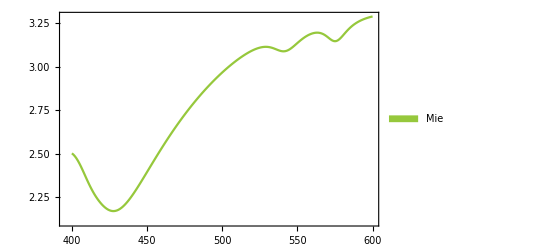

```mathematica
interpMie=ListPlot[eriQextMie,PlotStyle->verde,
              PlotLegends->Placed[SwatchLegend[{Style["Mie",FontFamily->"Latin Modern Roman 10",Magnification->1.1]},
                                                LegendMarkerSize->{15,5},
                                                LegendMargins->0,Spacings->0.05],{0.717,0.65}],
              Joined->True,
              Evaluate[Sequence @@ plotStyling]]
```

```mathematica
MinimalBy[eriQextMie,Last]
MaximalBy[eriQextMie1,Last]
MaximalBy[eriQextMie2,Last]
```

{{428,2.16421}}

{{529,3.11005}}

{{563,3.19352}}

### Matriz

```mathematica
dataMatrizCabs=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Matriz_Cabs.csv"];
dataMatrizCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Matriz_Csca.csv"];

dataQabsMatriz=Transpose[{dataMatrizCabs[[All,1]],dataMatrizCabs[[All,#]]/(Pi*2680^2)}]&/@Range[2,7];
dataQscaMatriz=Transpose[{dataMatrizCsca[[All,1]],dataMatrizCsca[[All,#]]/(Pi*2680^2)}]&/@Range[2,7];
```

```mathematica
dataMatrizCabs[[All,1]]
```

{400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,455,460,465,470,475,480,485,490,495,500,505,510,515,520,524,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,592,593,595,600}

```mathematica
eriQextMieResampled=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,dataMatrizCabs[[All,1]]}];
```

#### Rango total

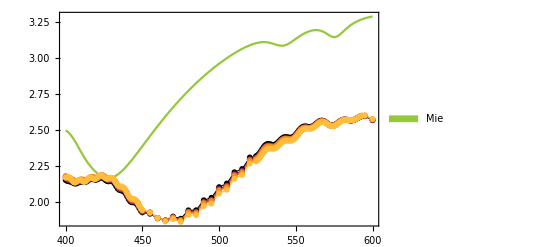

```mathematica
plotpointsMatriz=ListPlot[dataQext[dataQabsMatriz[[#]],dataQscaMatriz[[#]]]&/@Range[1,6],PlotMarkers->{"●",6},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"500","1000","1230","1470","1720","2300"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",2},
                                    LegendMargins->0,
                                    LegendLabel->Style[MaTeX["h\\:[\\mbox{nm}]"],FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.22,0.8}],
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ sunsetColors),
                      Evaluate[Sequence @@ plotStyling]];

ajusteMatriz=Show[{interpMie,plotpointsMatriz}, FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                PlotRange->All]
```

```mathematica
Export["ajusteMatriz.svg",ajusteMatriz]
```

ajusteMatriz.svg

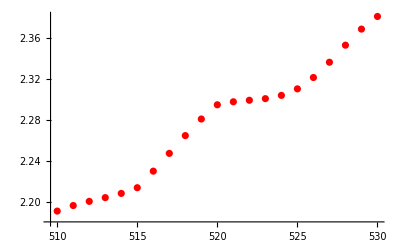

```mathematica
hola=Interpolation[Transpose[{dataMatrizCabs[[All,1]],dataQext[dataQabsMatriz[[2]],dataQscaMatriz[[2]]]}]];
hola2=Table[hola[x],{x,510,530}];
ListPlot[hola2, PlotStyle -> Red]
```

```mathematica
(*Modelo *)
modelo = a * Exp[-(x - x0)^2 / (2 * sigma^2)] + b;
ajuste = NonlinearModelFit[hola2, modelo, {{a,0.1}, {x0,565}, {sigma, 2}, b}, x];

{bestA, bestX0, bestSigma, bestB} = {a, x0, sigma, b} /. ajuste["BestFitParameters"];

(* 4. Calculamos el FWHM *)
fwhm = 2 * Sqrt[2 * Log[2]] * bestSigma
```

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

5.68153×10^64

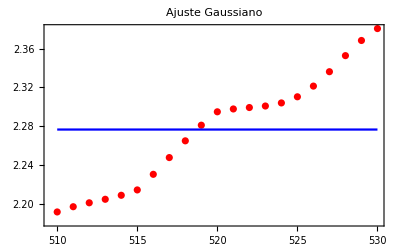

```mathematica
Show[
  ListPlot[hola2, PlotStyle -> Red, PlotLabel -> "Ajuste Gaussiano"],
  Plot[ajuste[x], {x, Min[hola2[[All, 1]]], Max[hola2[[All, 1]]]}, PlotStyle -> Blue],
  Frame -> True
]
```

#### Banda de Soret y bandas Q

```mathematica
matrizInterp=Interpolation[Transpose[{dataMatrizCabs[[All,1]],dataQext[dataQabsMatriz[[#]],dataQscaMatriz[[#]]][[All,2]]}]]&/@Range[1,6];
```

```mathematica
Mean[Abs[Table[matrizInterp[[#]][x],{x,400,600}]-eriQextMie]]&/@Range[1,6]
Abs[matrizInterp[[#]][541]-mieQext[nindexEriFit[541],Sqrt[1.823],2680,541][[4]]]&/@Range[1,6]
```

{{497.773,0.586425},{497.776,0.589889},{497.776,0.589194},{497.776,0.589429},{497.777,0.590824},{497.784,0.597754}}

{0.644582,0.653671,0.65507,0.657478,0.660806,0.673264}

```mathematica
ajusteMatrizSoret=Show[{interpMie,plotpointsMatriz}, FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                               PlotRange->{{405,450},{1.9,3}}]
```

-Graphics-

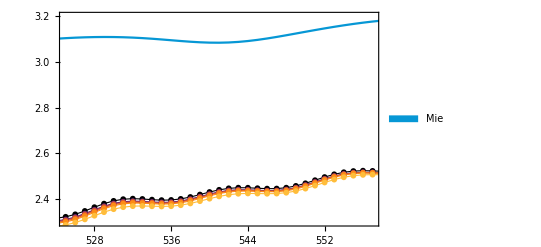

```mathematica
ajusteMatrizBeta=Show[{interpMie,plotpointsMatriz}, FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                PlotRange->{{525,557},{2.3,3.2}}]
```

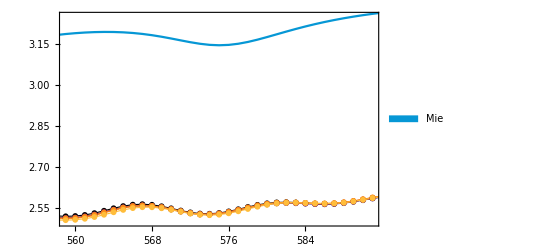

```mathematica
ajusteMatrizAlpha=Show[{interpMie,plotpointsMatriz}, FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                PlotRange->{{559,591},{2.5,3.25}}]
```

```mathematica
Export["ajusteMatrizSoret.svg",ajusteMatrizSoret]
Export["ajusteMatrizAlpha.svg",ajusteMatrizAlpha]
```

ajusteMatrizSoret.svg

ajusteMatrizAlpha.svg

```mathematica
Export["ajusteMatrizBeta.svg",ajusteMatrizBeta]
```

ajusteMatrizBeta.svg

### Mallado global

```mathematica
dataMeshCabs=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Global_mesh_Cabs.csv"];
dataMeshCsca=Import["C:\\Users\\danal\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Global_mesh_Csca.csv"];

dataQabsMeshGlobal=Transpose[{dataMeshCabs[[All,1]],dataMeshCabs[[All,#]]/(Pi*2680^2)}]&/@Range[2,6];
dataQscaMeshGlobal=Transpose[{dataMeshCsca[[All,1]],dataMeshCsca[[All,#]]/(Pi*2680^2)}]&/@Range[2,6];
```

```mathematica
eriQextMieResampled2=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,dataMeshCabs[[All,1]]}];
```

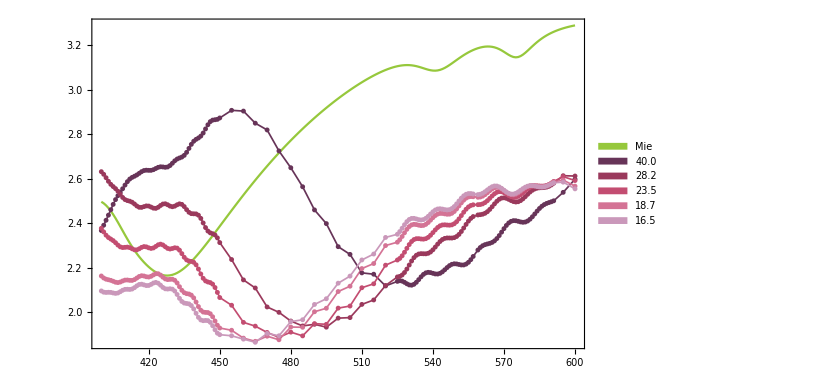

```mathematica
plotpointsMesh=ListPlot[dataQext[dataQabsMeshGlobal[[#]],dataQscaMeshGlobal[[#]]]&/@Range[1,5],PlotMarkers->{"●",5},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"40.0","28.2","23.5","18.7","16.5"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",3},
                                    LegendMargins->0,
                                    LegendLabel->Style["Tamaño mínimo de celda [nm]",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.38,0.8}],
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ candyColors),
                      Evaluate[Sequence @@ plotStyling]];

ajusteMesh=Show[{interpMie,plotpointsMesh}, FrameLabel->{{Style[MaTeX["Q_{\\text{ext}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                PlotRange->All]
```

```mathematica
MinimalBy[dataQext[dataQabsMeshGlobal[[5]],dataQscaMeshGlobal[[5]]],Last]
MinimalBy[eriQextMieResampled2,Last]
```

{{465,1.86448}}

{{428,2.16421}}

```mathematica
Mean[Abs[dataQext[dataQabsMeshGlobal[[5]],dataQscaMeshGlobal[[5]]][[All,2]]-eriQextMieResampled2[[All,2]]]]
```

0.499285

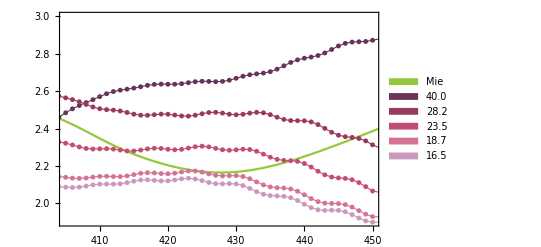

```mathematica
ajusteMeshSoret=Show[{interpMie,plotpointsMesh}, FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                PlotRange->{{405,450},{1.9,3}}]
```

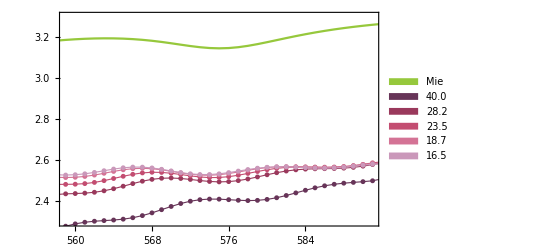

```mathematica
ajusteMeshAlpha=Show[{interpMie,plotpointsMesh}, FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                PlotRange->{{559,591},{2.3,3.3}}]
```

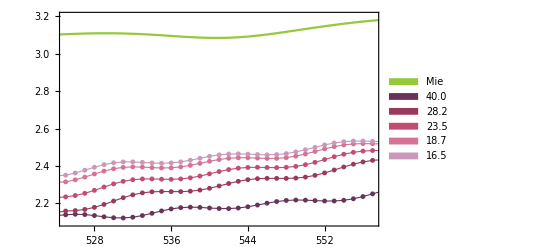

```mathematica
ajusteMeshBeta=Show[{interpMie,plotpointsMesh}, FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                               None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                PlotRange->{{525,557},{2.1,3.2}}]
```

```mathematica
Export["ajusteMeshSoret.svg",ajusteMeshSoret]
Export["ajusteMeshAlpha.svg",ajusteMeshAlpha]
Export["ajusteMeshBeta.svg",ajusteMeshBeta]
Export["ajusteMesh.svg",ajusteMesh]
```

```mathematica
meshGlobalInterp=Interpolation[Transpose[{dataMeshCabs[[All,1]],dataQext[dataQabsMeshGlobal[[#]],dataQscaMeshGlobal[[#]]][[All,2]]}]]&/@Range[1,5];
```

```mathematica
Mean[Abs[Table[meshGlobalInterp[[#]][x],{x,400,600}]-eriQextMie]]&/@Range[1,5]
Abs[matrizInterp[[#]][541]-mieQext[nindexEriFit[541],Sqrt[1.823],2680,541][[4]]]&/@Range[1,6]
```

```mathematica
0.5889498385933157-0.5875101366278531
```

0.0014397

### Mallado local - Superficie

El resultado en todos los casos es el mismo, tampoco cambia el tiempo de ejecución

### Mallado local - Volumen

```mathematica
dataMeshLocalCabs=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Local_mesh_Cabs.csv"];
dataMeshLocalCsca=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Local_mesh_Csca.csv"];

dataQabsMeshLocal=Transpose[{dataMeshLocalCabs[[All,1]],dataMeshLocalCabs[[All,#]]/(Pi*2680^2)}]&/@Range[2,6];
dataQscaMeshLocal=Transpose[{dataMeshLocalCsca[[All,1]],dataMeshLocalCsca[[All,#]]/(Pi*2680^2)}]&/@Range[2,6];

dataCabsMeshLocal=Transpose[{dataMeshLocalCabs[[All,1]],dataMeshLocalCabs[[All,#]]}]&/@Range[2,6];
dataCscaMeshLocal=Transpose[{dataMeshLocalCsca[[All,1]],dataMeshLocalCsca[[All,#]]}]&/@Range[2,6];
```

```mathematica
dataMeshLocalCabs[[All,1]]
```

{400,401,402,403,404,405,406,407,408,409,410,411,412,413,414,415,416,417,418,419,420,421,422,423,424,425,426,427,428,429,430,431,432,433,434,435,436,437,438,439,440,441,442,443,444,445,446,447,448,449,450,455,460,465,470,475,480,485,490,495,500,505,510,515,520,525,526,527,528,529,530,531,532,533,534,535,536,537,538,539,540,541,542,543,544,545,546,547,548,549,550,551,552,553,554,555,556,557,559,560,561,562,563,564,565,566,567,568,569,570,571,572,573,574,575,576,577,578,579,580,581,582,583,584,585,586,587,588,589,590,591,595,600}

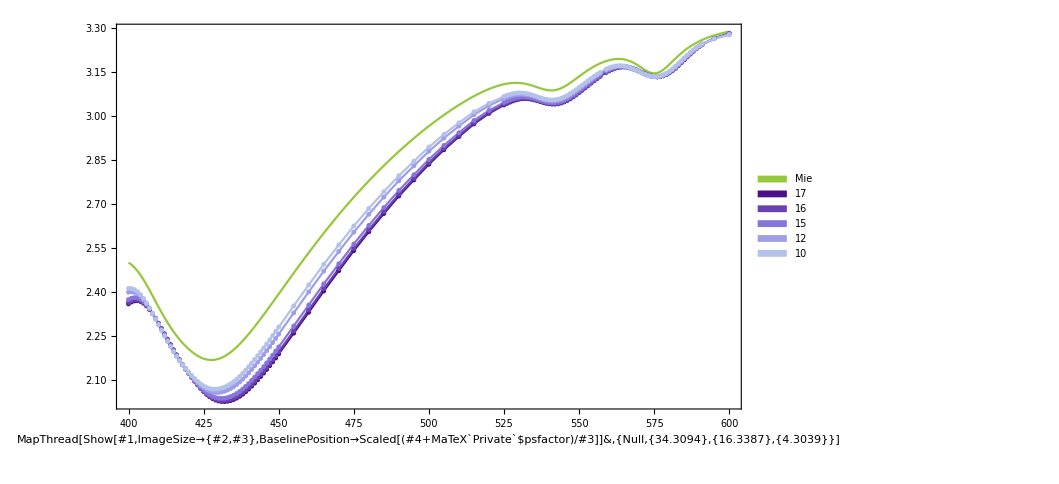

```mathematica
plotpointsMeshLocal=ListPlot[dataQext[dataQabsMeshLocal[[#]],dataQscaMeshLocal[[#]]]&/@Range[1,5],PlotMarkers->{"●",5},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"17","16","15","12","10"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",3},
                                    LegendMargins->0,
                                    LegendLabel->Style["Tamaño mínimo de celda [nm]",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.38,0.8}],
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ lakeColors),
                      Evaluate[Sequence @@ plotStyling]];

ajusteMeshLocal=Show[{interpMie,plotpointsMeshLocal}, FrameLabel->{{Style[MaTeX["Q_{\\text{ext}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                PlotRange->All]
```

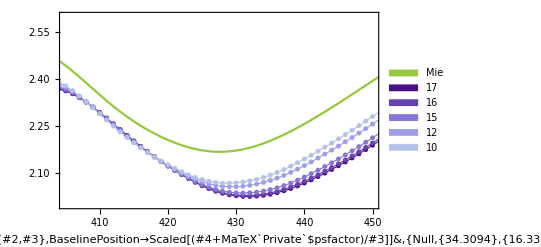

```mathematica
ajusteMeshLocalSoret=Show[{interpMie,plotpointsMeshLocal}, FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                PlotRange->{{405,450},{2,2.6}}]
```

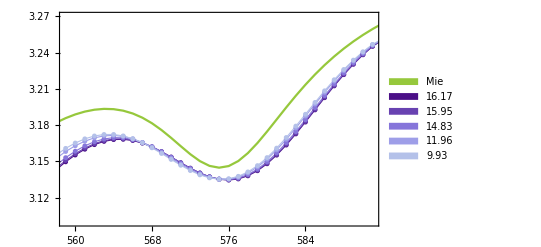

```mathematica
ajusteMeshLocalAlpha=Show[{interpMie,plotpointsMeshLocal}, 
                          FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                PlotRange->{{559,591},{3.1,3.27}}]
```

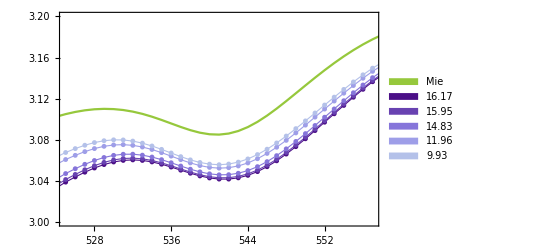

```mathematica
ajusteMeshLocalBeta=Show[{interpMie,plotpointsMeshLocal}, FrameLabel->{{Style[MaTeX["Q_{\\text{ext}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                PlotRange->{{525,557},{3,3.2}}]
```

```mathematica
Export["ajusteMeshLocal.svg",ajusteMeshLocal]
```

ajusteMeshLocal.svg

```mathematica
Export["ajusteMeshLocalSoret.svg",ajusteMeshLocalSoret]
Export["ajusteMeshLocalAlpha.svg",ajusteMeshLocalAlpha]
Export["ajusteMeshLocalBeta.svg",ajusteMeshLocalBeta]
Export["ajusteMeshLocal.svg",ajusteMeshLocal]
```

ajusteMeshLocalSoret.svg

ajusteMeshLocalAlpha.svg

ajusteMeshLocalBeta.svg

ajusteMeshLocal.svg

```mathematica
Length[dataQext[dataQabsMeshLocal[[5]],dataQscaMeshLocal[[5]]]]
Length[eriQextMieResampled]
```

133

136

#### Convergencia con Mie

```mathematica
eriQextMieResampled=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,dataMeshLocalCabs[[All,1]]}];
```

```mathematica
Mean[Abs[dataQext[dataQabsMeshLocal[[5]],dataQscaMeshLocal[[5]]]-eriQextMieResampled]]
```

{0,0.0531737}

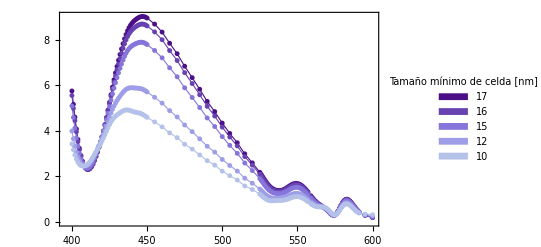

```mathematica
errorMeshLocalMie=ListPlot[{Transpose[{dataMeshLocalCabs[[All,1]],errorRel[eriQextMieResampled[[All,2]],dataQext[dataQabsMeshLocal[[1]],dataQscaMeshLocal[[1]]][[All,2]]]}],
                      Transpose[{dataMeshLocalCabs[[All,1]],errorRel[eriQextMieResampled[[All,2]],dataQext[dataQabsMeshLocal[[2]],dataQscaMeshLocal[[2]]][[All,2]]]}],
                      Transpose[{dataMeshLocalCabs[[All,1]],errorRel[eriQextMieResampled[[All,2]],dataQext[dataQabsMeshLocal[[3]],dataQscaMeshLocal[[3]]][[All,2]]]}],
                      Transpose[{dataMeshLocalCabs[[All,1]],errorRel[eriQextMieResampled[[All,2]],dataQext[dataQabsMeshLocal[[4]],dataQscaMeshLocal[[4]]][[All,2]]]}],
                      Transpose[{dataMeshLocalCabs[[All,1]],errorRel[eriQextMieResampled[[All,2]],dataQext[dataQabsMeshLocal[[5]],dataQscaMeshLocal[[5]]][[All,2]]]}]},
                      PlotMarkers->{"●",5},
                      FrameLabel->{{Style[MaTeX["100(Q_{\\text{ext}}^{\\text{Mie}}-Q_{\\text{ext}}^{\\text{CST}})/Q_{\\text{ext}}^{\\text{Mie}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ lakeColors),
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"17","16","15","12","10"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",3},
                                    LegendMargins->0,
                                    LegendLabel->Style["Tamaño mínimo de celda [nm]",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.62,0.8}],
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["errorMeshLocal.svg",errorMeshLocalMie]
```

errorMeshLocal.svg

#### Convergencia numérica

```mathematica
Mean[errorRel[dataQext[dataQabsMeshLocal[[5]],dataQscaMeshLocal[[5]]],dataQext[dataQabsMeshLocal[[4]],dataQscaMeshLocal[[4]]]]]
Mean[errorRel[dataQext[dataQabsMeshLocal[[5]],dataQscaMeshLocal[[5]]],]]
```

{0,0.297812}

{1/133 ((100 Abs[400-Null])/Null+(100 Abs[401-Null])/Null+(100 Abs[402-Null])/Null+(100 Abs[403-Null])/Null+(100 Abs[404-Null])/Null+(100 Abs[405-Null])/Null+(100 Abs[406-Null])/Null+(100 Abs[407-Null])/Null+(100 Abs[408-Null])/Null+(100 Abs[409-Null])/Null+(100 Abs[410-Null])/Null+(100 Abs[411-Null])/Null+(100 Abs[412-Null])/Null+(100 Abs[413-Null])/Null+(100 Abs[414-Null])/Null+(100 Abs[415-Null])/Null+(100 Abs[416-Null])/Null+(100 Abs[417-Null])/Null+(100 Abs[418-Null])/Null+(100 Abs[419-Null])/Null+(100 Abs[420-Null])/Null+(100 Abs[421-Null])/Null+(100 Abs[422-Null])/Null+(100 Abs[423-Null])/Null+(100 Abs[424-Null])/Null+(100 Abs[425-Null])/Null+(100 Abs[426-Null])/Null+(100 Abs[427-Null])/Null+(100 Abs[428-Null])/Null+(100 Abs[429-Null])/Null+(100 Abs[430-Null])/Null+(100 Abs[431-Null])/Null+(100 Abs[432-Null])/Null+(100 Abs[433-Null])/Null+(100 Abs[434-Null])/Null+(100 Abs[435-Null])/Null+(100 Abs[436-Null])/Null+(100 Abs[437-Null])/Null+(100 Abs[438-Null])/Null+(100 Abs[439-Null])/Null+(100 Abs[440-Null])/Null+(100 Abs[441-Null])/Null+(100 Abs[442-Null])/Null+(100 Abs[443-Null])/Null+(100 Abs[444-Null])/Null+(100 Abs[445-Null])/Null+(100 Abs[446-Null])/Null+(100 Abs[447-Null])/Null+(100 Abs[448-Null])/Null+(100 Abs[449-Null])/Null+(100 Abs[450-Null])/Null+(100 Abs[455-Null])/Null+(100 Abs[460-Null])/Null+(100 Abs[465-Null])/Null+(100 Abs[470-Null])/Null+(100 Abs[475-Null])/Null+(100 Abs[480-Null])/Null+(100 Abs[485-Null])/Null+(100 Abs[490-Null])/Null+(100 Abs[495-Null])/Null+(100 Abs[500-Null])/Null+(100 Abs[505-Null])/Null+(100 Abs[510-Null])/Null+(100 Abs[515-Null])/Null+(100 Abs[520-Null])/Null+(100 Abs[525-Null])/Null+(100 Abs[526-Null])/Null+(100 Abs[527-Null])/Null+(100 Abs[528-Null])/Null+(100 Abs[529-Null])/Null+(100 Abs[530-Null])/Null+(100 Abs[531-Null])/Null+(100 Abs[532-Null])/Null+(100 Abs[533-Null])/Null+(100 Abs[534-Null])/Null+(100 Abs[535-Null])/Null+(100 Abs[536-Null])/Null+(100 Abs[537-Null])/Null+(100 Abs[538-Null])/Null+(100 Abs[539-Null])/Null+(100 Abs[540-Null])/Null+(100 Abs[541-Null])/Null+(100 Abs[542-Null])/Null+(100 Abs[543-Null])/Null+(100 Abs[544-Null])/Null+(100 Abs[545-Null])/Null+(100 Abs[546-Null])/Null+(100 Abs[547-Null])/Null+(100 Abs[548-Null])/Null+(100 Abs[549-Null])/Null+(100 Abs[550-Null])/Null+(100 Abs[551-Null])/Null+(100 Abs[552-Null])/Null+(100 Abs[553-Null])/Null+(100 Abs[554-Null])/Null+(100 Abs[555-Null])/Null+(100 Abs[556-Null])/Null+(100 Abs[557-Null])/Null+(100 Abs[559-Null])/Null+(100 Abs[560-Null])/Null+(100 Abs[561-Null])/Null+(100 Abs[562-Null])/Null+(100 Abs[563-Null])/Null+(100 Abs[564-Null])/Null+(100 Abs[565-Null])/Null+(100 Abs[566-Null])/Null+(100 Abs[567-Null])/Null+(100 Abs[568-Null])/Null+(100 Abs[569-Null])/Null+(100 Abs[570-Null])/Null+(100 Abs[571-Null])/Null+(100 Abs[572-Null])/Null+(100 Abs[573-Null])/Null+(100 Abs[574-Null])/Null+(100 Abs[575-Null])/Null+(100 Abs[576-Null])/Null+(100 Abs[577-Null])/Null+(100 Abs[578-Null])/Null+(100 Abs[579-Null])/Null+(100 Abs[580-Null])/Null+(100 Abs[581-Null])/Null+(100 Abs[582-Null])/Null+(100 Abs[583-Null])/Null+(100 Abs[584-Null])/Null+(100 Abs[585-Null])/Null+(100 Abs[586-Null])/Null+(100 Abs[587-Null])/Null+(100 Abs[588-Null])/Null+(100 Abs[589-Null])/Null+(100 Abs[590-Null])/Null+(100 Abs[591-Null])/Null+(100 Abs[595-Null])/Null+(100 Abs[600-Null])/Null),1/133 ((100 Abs[2.0692-Null])/Null+(100 Abs[2.06953-Null])/Null+(100 Abs[2.07035-Null])/Null+(100 Abs[2.07149-Null])/Null+(100 Abs[2.07285-Null])/Null+(100 Abs[2.07516-Null])/Null+(100 Abs[2.0766-Null])/Null+(100 Abs[2.08054-Null])/Null+(100 Abs[2.08152-Null])/Null+(100 Abs[2.08754-Null])/Null+(100 Abs[2.08761-Null])/Null+(100 Abs[2.09485-Null])/Null+(100 Abs[2.09597-Null])/Null+(100 Abs[2.10322-Null])/Null+(100 Abs[2.10562-Null])/Null+(100 Abs[2.11265-Null])/Null+(100 Abs[2.11624-Null])/Null+(100 Abs[2.12302-Null])/Null+(100 Abs[2.12769-Null])/Null+(100 Abs[2.13417-Null])/Null+(100 Abs[2.13991-Null])/Null+(100 Abs[2.14592-Null])/Null+(100 Abs[2.15292-Null])/Null+(100 Abs[2.15812-Null])/Null+(100 Abs[2.16681-Null])/Null+(100 Abs[2.17065-Null])/Null+(100 Abs[2.18169-Null])/Null+(100 Abs[2.18345-Null])/Null+(100 Abs[2.19652-Null])/Null+(100 Abs[2.19759-Null])/Null+(100 Abs[2.20988-Null])/Null+(100 Abs[2.2145-Null])/Null+(100 Abs[2.22356-Null])/Null+(100 Abs[2.23231-Null])/Null+(100 Abs[2.23756-Null])/Null+(100 Abs[2.25085-Null])/Null+(100 Abs[2.25187-Null])/Null+(100 Abs[2.26639-Null])/Null+(100 Abs[2.26991-Null])/Null+(100 Abs[2.28105-Null])/Null+(100 Abs[2.28925-Null])/Null+(100 Abs[2.30862-Null])/Null+(100 Abs[2.3277-Null])/Null+(100 Abs[2.34608-Null])/Null+(100 Abs[2.35345-Null])/Null+(100 Abs[2.36326-Null])/Null+(100 Abs[2.37865-Null])/Null+(100 Abs[2.39166-Null])/Null+(100 Abs[2.4018-Null])/Null+(100 Abs[2.40878-Null])/Null+(100 Abs[2.41255-Null])/Null+(100 Abs[2.41325-Null])/Null+(100 Abs[2.4251-Null])/Null+(100 Abs[2.49528-Null])/Null+(100 Abs[2.56134-Null])/Null+(100 Abs[2.62608-Null])/Null+(100 Abs[2.68566-Null])/Null+(100 Abs[2.74317-Null])/Null+(100 Abs[2.79732-Null])/Null+(100 Abs[2.8468-Null])/Null+(100 Abs[2.89517-Null])/Null+(100 Abs[2.93832-Null])/Null+(100 Abs[2.97796-Null])/Null+(100 Abs[3.01542-Null])/Null+(100 Abs[3.04463-Null])/Null+(100 Abs[3.05567-Null])/Null+(100 Abs[3.05622-Null])/Null+(100 Abs[3.05631-Null])/Null+(100 Abs[3.05786-Null])/Null+(100 Abs[3.0582-Null])/Null+(100 Abs[3.06038-Null])/Null+(100 Abs[3.0613-Null])/Null+(100 Abs[3.06354-Null])/Null+(100 Abs[3.06554-Null])/Null+(100 Abs[3.06706-Null])/Null+(100 Abs[3.06756-Null])/Null+(100 Abs[3.07061-Null])/Null+(100 Abs[3.07077-Null])/Null+(100 Abs[3.07135-Null])/Null+(100 Abs[3.0739-Null])/Null+(100 Abs[3.07462-Null])/Null+(100 Abs[3.07666-Null])/Null+(100 Abs[3.07684-Null])/Null+(100 Abs[3.07722-Null])/Null+(100 Abs[3.07867-Null])/Null+(100 Abs[3.07902-Null])/Null+(100 Abs[3.07977-Null])/Null+(100 Abs[3.07989-Null])/Null+(100 Abs[3.08357-Null])/Null+(100 Abs[3.09078-Null])/Null+(100 Abs[3.09831-Null])/Null+(100 Abs[3.10601-Null])/Null+(100 Abs[3.11375-Null])/Null+(100 Abs[3.12144-Null])/Null+(100 Abs[3.12896-Null])/Null+(100 Abs[3.13531-Null])/Null+(100 Abs[3.13569-Null])/Null+(100 Abs[3.13624-Null])/Null+(100 Abs[3.13645-Null])/Null+(100 Abs[3.1377-Null])/Null+(100 Abs[3.13893-Null])/Null+(100 Abs[3.14135-Null])/Null+(100 Abs[3.1425-Null])/Null+(100 Abs[3.14318-Null])/Null+(100 Abs[3.14657-Null])/Null+(100 Abs[3.14687-Null])/Null+(100 Abs[3.14966-Null])/Null+(100 Abs[3.15169-Null])/Null+(100 Abs[3.1532-Null])/Null+(100 Abs[3.15661-Null])/Null+(100 Abs[3.16084-Null])/Null+(100 Abs[3.16105-Null])/Null+(100 Abs[3.1613-Null])/Null+(100 Abs[3.16526-Null])/Null+(100 Abs[3.16545-Null])/Null+(100 Abs[3.16872-Null])/Null+(100 Abs[3.1688-Null])/Null+(100 Abs[3.16983-Null])/Null+(100 Abs[3.17111-Null])/Null+(100 Abs[3.17114-Null])/Null+(100 Abs[3.17233-Null])/Null+(100 Abs[3.17234-Null])/Null+(100 Abs[3.17927-Null])/Null+(100 Abs[3.18905-Null])/Null+(100 Abs[3.19887-Null])/Null+(100 Abs[3.20847-Null])/Null+(100 Abs[3.21761-Null])/Null+(100 Abs[3.22612-Null])/Null+(100 Abs[3.23386-Null])/Null+(100 Abs[3.24078-Null])/Null+(100 Abs[3.24686-Null])/Null+(100 Abs[3.26414-Null])/Null+(100 Abs[3.27811-Null])/Null)}

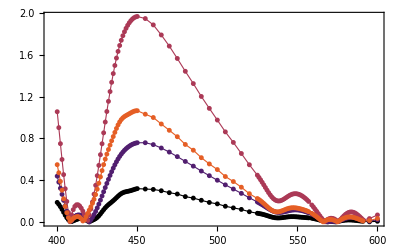

```mathematica
plotpointsMeshLocalNumeric=ListPlot[{Transpose[{dataMeshLocalCabs[[All,1]],errorRel[dataQext[dataQabsMeshLocal[[2]],dataQscaMeshLocal[[2]]][[All,2]],
                                                                                                dataQext[dataQabsMeshLocal[[1]],dataQscaMeshLocal[[1]]][[All,2]]]}],
                      Transpose[{dataMeshLocalCabs[[All,1]],errorRel[dataQext[dataQabsMeshLocal[[3]],dataQscaMeshLocal[[3]]][[All,2]],
                                                                                                dataQext[dataQabsMeshLocal[[2]],dataQscaMeshLocal[[2]]][[All,2]]]}],
                      Transpose[{dataMeshLocalCabs[[All,1]],errorRel[dataQext[dataQabsMeshLocal[[4]],dataQscaMeshLocal[[4]]][[All,2]],
                                                                                                dataQext[dataQabsMeshLocal[[3]],dataQscaMeshLocal[[3]]][[All,2]]]}],
                      Transpose[{dataMeshLocalCabs[[All,1]],errorRel[dataQext[dataQabsMeshLocal[[5]],dataQscaMeshLocal[[5]]][[All,2]],
                                                                                                dataQext[dataQabsMeshLocal[[4]],dataQscaMeshLocal[[4]]][[All,2]]]}]
                      },
                      PlotMarkers->{"●",5},
                      FrameLabel->{{Style[MaTeX["100(Q_{\\text{ext}}^{\\text{Mie}}-Q_{\\text{ext}}^{\\text{CST}})/Q_{\\text{ext}}^{\\text{Mie}} "],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                Style[MaTeX["\\hbar\\omega\\: [\\mbox{eV}]"],Magnification->1.4]}},
                                FrameTicks->{{Automatic,None},{Automatic,Charting`ScaledTicks[{h c/# &, h c/# &}]}},
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ sunsetColors),
                      Evaluate[Sequence @@ plotStyling]]
```

### PML

El resultado en todos los casos es el mismo, solo cambia el tiempo de ejecución

```mathematica
dataPMLCabs=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\PML_Cabs.csv"];
dataPMLCsca=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\PML_Ccsa.csv"];

dataQabsPML=Transpose[{dataPMLCabs[[All,1]],dataPMLCabs[[All,#]]/(Pi*2680^2)}]&/@Range[2,5];
dataQscaPML=Transpose[{dataPMLCsca[[All,1]],dataPMLCsca[[All,#]]/(Pi*2680^2)}]&/@Range[2,5];

dataCabsPML=Transpose[{dataPMLCabs[[All,1]],dataPMLCabs[[All,#]]}]&/@Range[2,5];
dataCscaPML=Transpose[{dataPMLCsca[[All,1]],dataPMLCsca[[All,#]]}]&/@Range[2,5];
```

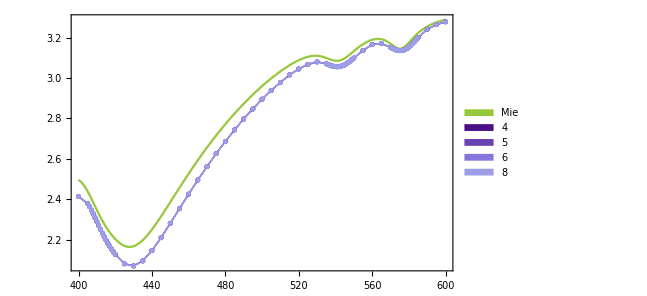

```mathematica
plotpointsPML=ListPlot[dataQext[dataQabsPML[[#]],dataQscaPML[[#]]]&/@Range[1,4],PlotMarkers->{"●",5},
                      PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"4","5","6","8"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",3},
                                    LegendMargins->0,
                                    LegendLabel->Style["Tamaño mínimo de celda [nm]",FontFamily->"Latin Modern Roman 10",Magnification->1.1],
                                    Spacings->0.05],{0.38,0.8}],
                      Joined->True,
                      PlotStyle -> (Directive[#, Thickness[0.002]] & /@ lakeColors),
                      Evaluate[Sequence @@ plotStyling]];

ajustePML=Show[{interpMie,plotpointsPML}, FrameLabel->{{Style[MaTeX["Q_{\\text{ext}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
                                FrameTicks->{{Automatic,None},{Automatic,None}},
                                PlotRange->All]
```

```mathematica
dataQext[dataQabsPML[[4]],dataQscaPML[[4]]]
```

{{400,2.41327},{405,2.37867},{406,2.36328},{407,2.3461},{408,2.32771},{409,2.30863},{410,2.28926},{411,2.26992},{412,2.25086},{413,2.23232},{414,2.21451},{415,2.19759},{416,2.18168},{417,2.16681},{418,2.15291},{419,2.1399},{420,2.12768},{425,2.08052},{430,2.07033},{435,2.09484},{440,2.14592},{445,2.20989},{450,2.28106},{455,2.35346},{460,2.42511},{465,2.49528},{470,2.56135},{475,2.62606},{480,2.68565},{485,2.74316},{490,2.79731},{495,2.8468},{500,2.89517},{505,2.93832},{510,2.97797},{515,3.01542},{520,3.04462},{525,3.06757},{530,3.07988},{535,3.07059},{536,3.06704},{537,3.06353},{538,3.06037},{539,3.05785},{540,3.05622},{541,3.05567},{542,3.05631},{543,3.05819},{544,3.0613},{545,3.06553},{546,3.07076},{547,3.07683},{548,3.08356},{549,3.09076},{550,3.09829},{555,3.13624},{560,3.16527},{565,3.17113},{570,3.15169},{571,3.14687},{572,3.14251},{573,3.13894},{574,3.13646},{575,3.13533},{576,3.13571},{577,3.13772},{578,3.14137},{579,3.14658},{580,3.15321},{581,3.16105},{582,3.16984},{583,3.17927},{584,3.18905},{585,3.19887},{590,3.24079},{595,3.26416},{600,3.27811}}

```mathematica
Abs[mieQsca[nindexEriFit[435],Sqrt[1.823],2680,435][[4]] - 2.0950874907931776]
Abs[mieQsca[nindexEriFit[435],Sqrt[1.823],2680,435][[4]]-2.094852700024964]
Abs[mieQsca[nindexEriFit[435],Sqrt[1.823],2680,435][[4]]-2.0948469874296856]
Abs[mieQsca[nindexEriFit[435],Sqrt[1.823],2680,435][[4]]-2.0948430382491945]
```

0.431579

0.431344

0.431339

0.431335

```mathematica
PML={4,5,6,8}
capas={4,5,6,7}
grosor={68.2575,85.3218,102.386,136.515}
```

### Tiempos

```mathematica
N[4918/60]
```

81.9667

```mathematica
tiemposMatriz={4128,4918,5386,5825,6461,7888} (*segundos*);
matrices={500,1000,1230,1470,1720,2300};
tiemposGlobal={443,1332,2368,5132,8022} (*segundos*);
global={7,10,12,15,17};
tamañoCeldaGlobal={40.0,28.2,23.5,18.7,16.5};
tiemposPML={49027,47791,46921,46277} (*segundos*);
pml={0.0001,0.01,0.1,1};
tiemposLocal={86483,15986,7831,6409,6237} (*segundos*);
local={10,12,15,16,20};
tamañoCeldaLocal={9.93,11.96,14.83,15.95,16.17};
```

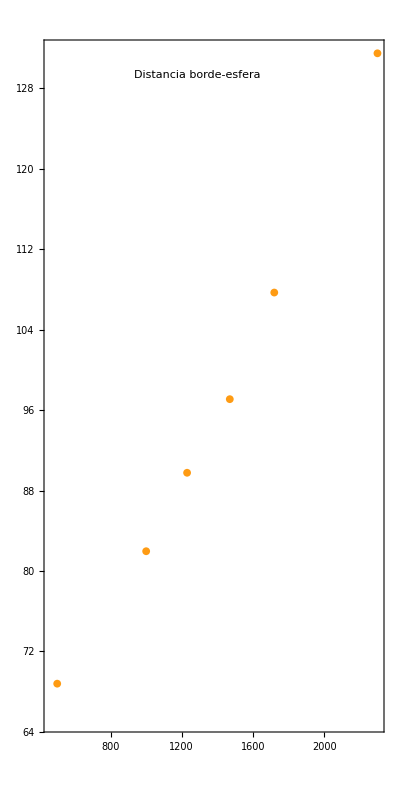

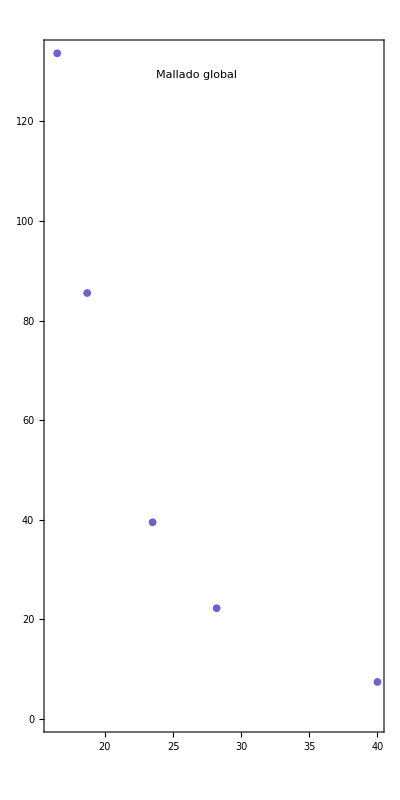

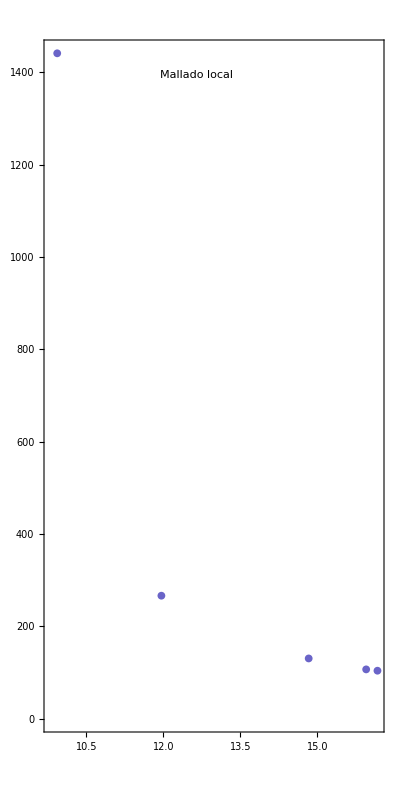

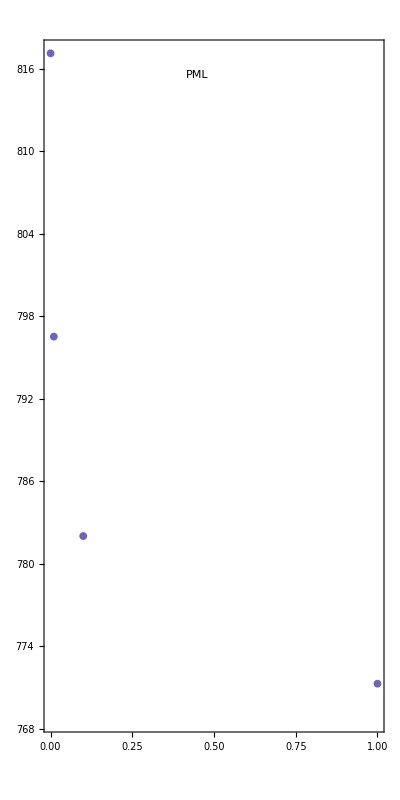

```mathematica
plotTiemposMatriz=ListPlot[Transpose[{matrices,tiemposMatriz/60}],PlotMarkers->{"●",8},
                      PlotStyle->solarColors,
                      AspectRatio->2,
                      FrameLabel->{{Style[MaTeX["\\text{Tiempo de ejecución [min]}"],Magnification->1.4],None},
                                {Style[MaTeX["h\\text{ [nm]}"],Magnification->1.4],None}},
                      FrameTicks->{{Automatic,None},{Automatic,None}},
                      PlotRange->All,
                      ImagePadding->{{90,12},{60,10}},
                      Epilog->Inset[Style["Distancia borde-esfera",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.45,0.95}]],
                      Evaluate[Sequence @@ plotStyling]]
                      
plotTiemposMeshGlobal=ListPlot[Transpose[{tamañoCeldaGlobal,tiemposGlobal/60}],PlotMarkers->{"●",8},
                      PlotStyle->colors,
                      AspectRatio->2,
                      FrameLabel->{{Style[MaTeX["\\text{Tiempo de ejecución [min]}"],Magnification->1.4],None},
                                {Style[MaTeX["\\text{Tamaño mínimo de celda [nm]}"],Magnification->1.4],None}},
                      FrameTicks->{{Automatic,None},{Automatic,None}},
                      PlotRange->All,
                      ImagePadding->{{90,30},{60,10}},
                      Epilog->Inset[Style["Mallado global",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.45,0.95}]],
                      Evaluate[Sequence @@ plotStyling]]

plotTiemposMeshLocal=ListPlot[Transpose[{tamañoCeldaLocal,tiemposLocal/60}],PlotMarkers->{"●",8},
                      PlotStyle->colors,
                      AspectRatio->2,
                      FrameLabel->{{Style[MaTeX["\\text{Tiempo de ejecución [min]}"],Magnification->1.4],None},
                                {Style[MaTeX["\\text{Tamaño mínimo de celda [nm]}"],Magnification->1.4],None}},
                      FrameTicks->{{Automatic,None},{Automatic,None}},
                      PlotRange->All,
                      Epilog->Inset[Style["Mallado local",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.45,0.95}]],
                      ImagePadding->{{90,45},{60,10}},
                      Evaluate[Sequence @@ plotStyling]]
                      
                      
plotTiemposPML=ListPlot[Transpose[{pml,tiemposPML/60}],PlotMarkers->{"●",8},
                      PlotStyle->colors,
                      AspectRatio->2,
                      FrameLabel->{{Style[MaTeX["\\text{Tiempo de ejecución [min]}"],Magnification->1.4],None},
                                {Style[MaTeX["\\text{Nivel de reflexión}\\times 10^{-4}"],Magnification->1.4],None}},
                      FrameTicks->{{Automatic,None},{Automatic,None}},
                      PlotRange->All,
                      Epilog->Inset[Style["PML",Black,FontFamily->"Latin Modern Roman 10",Magnification->1.4],Scaled[{0.45,0.95}]],
                      ImagePadding->{{90,30},{60,10}},
                      Evaluate[Sequence @@ plotStyling]]
```

```mathematica
Export["plotTiemposMeshGlobal.svg",plotTiemposMeshGlobal]
```

plotTiemposMeshGlobal.svg

plotTiemposMeshLocal.svg

plotTiemposPML.svg

```mathematica
Export["plotTiemposMatriz.svg",plotTiemposMatriz]
```

plotTiemposMatriz.svg

```mathematica
Export["plotTiemposMeshLocal.svg",plotTiemposMeshLocal]
Export["plotTiemposPML.svg",plotTiemposPML]
```

plotTiemposMeshLocal.svg

plotTiemposPML.svg

### Variación de h con mesh volumen

```mathematica
lambdas={428,529,563};
cabs1050=Transpose[{lambdas,{14679675.786179,3181382.5580966,3175560.7440500}/(Pi*(2680)^2)}];
csca1050=Transpose[{lambdas,{31988425.079743,66283271.164158,68405183.450969}/(Pi*(2680)^2)}];
cabs1000=Transpose[{lambdas,{14676860.52,3180388.711,3175818.866}/(Pi*2680^2)}]
csca1000=Transpose[{lambdas,{32020453.58,66295062.51,68405129.85}/(Pi*2680^2)}]
cabs950=Transpose[{lambdas,{14675326.696537,3181869.2834988,3177523.7479061}/(Pi*(2680)^2)}];
csca950=Transpose[{lambdas,{32051529.254346,66302861.888600,68401720.068415}/(Pi*(2680)^2)}];
```

{{428,0.65045},{529,0.140949},{563,0.140746}}

{{428,1.41908},{529,2.93807},{563,3.03158}}

```mathematica
qext1050=dataQext[cabs1050,csca1050]
qext1000=dataQext[cabs1000,csca1000]
qext950=dataQext[cabs950,csca950]

eriQextMiepruebas=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,lambdas}];

error1050=errorRel[eriQextMiepruebas[[All,2]],qext1050[[All,2]]]
error1000=errorRel[eriQextMiepruebas[[All,2]],qext1000[[All,2]]]
error950=errorRel[eriQextMiepruebas[[All,2]],qext950[[All,2]]]
```

{{428,2.06824},{529,3.07854},{563,3.17232}}

{{428,2.06953},{529,3.07902},{563,3.17233}}

{{428,2.07084},{529,3.07943},{563,3.17225}}

{4.64005,1.0235,0.668434}

{4.57459,1.0078,0.668147}

{4.50847,0.994313,0.670544}

```mathematica
{{428,2.06953340613939704},{529,2.0695334061399704},{563,3.172327305457468}}
```

{{428,2.07084},{529,3.07943},{563,3.17225}}

{4.57459,1.0078,0.668147}

```mathematica
100*Abs[2.250241423483381-1.9069399358480061]/1.9069399358480061
```

18.0027

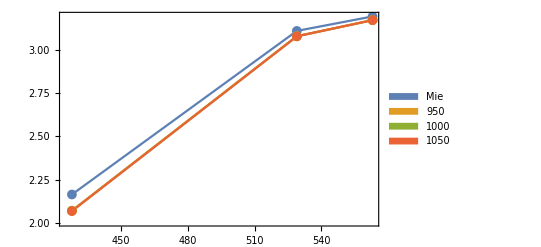

```mathematica
errorfinalh=ListPlot[{eriQextMiepruebas,qext950,qext1000,qext1050},PlotRange->All,PlotMarkers->{"●",10},Joined->True,
          Frame->True,
        FrameLabel->{{Style[MaTeX["Q_{\\text{ext}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
        FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
        LabelStyle->{FontFamily->"Latin Modern Roman 10"},
        FrameTicks->{{Automatic,None},{Automatic,None}},
        ImagePadding->{{90,10},{60,60}},
        PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"Mie","950","1000","1050"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",3},
                                    LegendMargins->0,
                                    Spacings->0.05],{0.2,0.8}]]
```

```mathematica
Export["errorfinalh.svg",errorfinalh]
```

errorfinalh.svg

### Variación de mesh global

```mathematica
lambdas2={428,529,563};
cabs17=Transpose[{lambdas,{14724446.461158,3187915.4788448,3182491.8178187}/(Pi*(2680)^2)}];
csca17=Transpose[{lambdas,{32183757.475449,66396433.309250,68455113.726960}/(Pi*(2680)^2)}];
cabs15=Transpose[{lambdas,{14676860.52,3180388.711,3175818.866}/(Pi*2680^2)}];
csca15=Transpose[{lambdas,{32020453.58,66295062.51,68405129.85}/(Pi*2680^2)}];
cabs12=Transpose[{lambdas,{14553281.685433,3163806.7746234,3159228.1085573}/(Pi*(2680)^2)}];
csca12=Transpose[{lambdas,{31504763.352600,65986416.636173,68244064.268133}/(Pi*(2680)^2)}];
```

```mathematica
eriQextMiepruebas2=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,lambdas2}];

qext17=dataQext[cabs17,csca17]
qext15=dataQext[cabs15,csca15]
qext12=dataQext[cabs12,csca12]

error17=errorRel[eriQextMiepruebas2[[All,2]],qext17[[All,2]]]
error15=errorRel[eriQextMiepruebas2[[All,2]],qext15[[All,2]]]
error12=errorRel[eriQextMiepruebas2[[All,2]],qext12[[All,2]]]
```

{{428,2.07888},{529,3.08384},{563,3.17484}}

{{428,2.06953},{529,3.07902},{563,3.17233}}

{{428,2.0412},{529,3.0646},{563,3.16445}}

{4.10444,0.849729,0.58853}

{4.57459,1.0078,0.668147}

{6.02605,1.48286,0.918616}

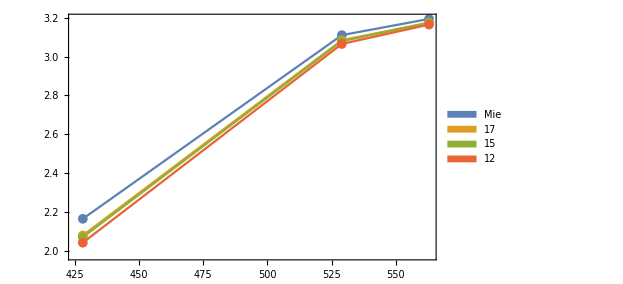

```mathematica
errorfinalMeshGlobal=ListPlot[{eriQextMiepruebas2,qext17,qext15,qext12},Joined->True,PlotRange->All,PlotMarkers->{"●",10},
         Frame->True,
        FrameLabel->{{Style[MaTeX["Q_{\\text{ext}}"],Magnification->1.4],None},
                                {Style[MaTeX["\\lambda\\:[\\mbox{nm}]"],Magnification->1.4],
                                None}},
        FrameStyle->Directive[Black,FontFamily->"Latin Modern Roman 10",Magnification->1.6],
        LabelStyle->{FontFamily->"Latin Modern Roman 10"},
        FrameTicks->{{Automatic,None},{Automatic,None}},
        PlotLegends->Placed[SwatchLegend[Style[#,FontFamily->"Latin Modern Roman 10",Magnification->1.1]&/@{"Mie","17","15","12"},
                                    LegendMarkerSize->{15,5},
                                    LegendLayout->{"Column",3},
                                    LegendMargins->0,
                                    Spacings->0.05],{0.2,0.8}],
        ImagePadding->{{90,10},{60,60}}]
```

```mathematica
Export["errorfinalMeshGlobal.svg",errorfinalMeshGlobal]
```

errorfinalMeshGlobal.svg

### Mie - Microcito

```mathematica
eriQabsMieEsf=Table[{λ,mieQabs[Sqrt[partere342[h c/λ]+ I fit34tot[h c/λ]],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,1}];
eriQscaMieEsf=Table[{λ,mieQsca[Sqrt[partere342[h c/λ]+ I fit34tot[h c/λ]],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,1}];
eriQextMieEsf=Table[{λ,mieQext[Sqrt[partere342[h c/λ]+ I fit34tot[h c/λ]],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,1}];
```

```mathematica
dataCabsCscaEsf=Import["C:\\Users\\danal\\Documents\\Github\\Tesis-de-Licenciatura\\CST\\Resultados\\Esferocito_Cabs_Csca.csv"];
```

```mathematica
dataQabsEsf=Transpose[{dataCabsCscaEsf[[All,1]],dataCabsCscaEsf[[All,2]]/(Pi*2680^2)}];
dataQscaEsf=Transpose[{dataCabsCscaEsf[[All,1]],dataCabsCscaEsf[[All,3]]/(Pi*2680^2)}];
```

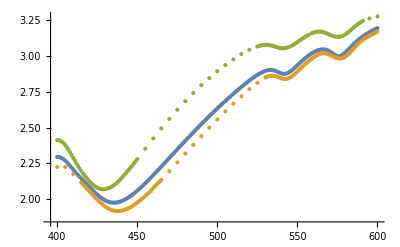

```mathematica
ListPlot[{eriQextMieEsf,dataQext[dataQabsEsf,dataQscaEsf],dataQext[dataQabsMeshLocal[[5]],dataQscaMeshLocal[[5]]]}]
```